## Survival plots

What this plotting code generates : 
List Step Plots that show the survival of a event over time 
Input file : Excel sheet with data ...

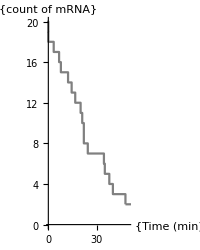
```mathematica
(*-Graphics- *)
```

### Data input *Drag and drop excel sheet into a variable named “data” below...

```mathematica
data = {{{"","","","","",""},{"","","","",1.1111111111111112,"<- min per frame"},{"","","","*60 means spot never disappeared","",""},{"cell","trackN","frame B appears","frame G disappears","time B appears","time G disappears"},{6.,1.,0.,999.,0.,1110.},{7.,2.,0.,999.,0.,1110.},{9.,3.,0.,999.,0.,1110.},{9.,12.,0.,999.,0.,1110.},{10.,20.,0.,999.,0.,1110.},{"bc793 presentation cell","*fix w exact numbers!! ","","",0.,1110.},{"","","","","",""},{"","","","","",""},{"","","","","",""},{"","","","","",""},{"","","","","",""},{"","","","","",""},{"","","","","",""},{"","","","","",""},{"","","","","",""},{"","","","","",""},{"","","","","",""}},{{"","","","","","",""},{"",1.1111111111111112,"<- min per frame","","frame","Min","#spots"},{"","","","",0.,0.,6.},{"time B appears","time G disappears","G aligned to B","",1.,0.8999999999999999,6.},{0.,1110.,1110.,"",2.,1.7999999999999998,6.},{0.,1110.,1110.,"",3.,2.6999999999999997,6.},{0.,1110.,1110.,"",4.,3.5999999999999996,6.},{0.,1110.,1110.,"",5.,4.5,6.},{0.,1110.,1110.,"",6.,5.3999999999999995,6.},{0.,1110.,1110.,"",7.,6.3,6.},{"","","","",8.,7.199999999999999,6.},{"","","","",9.,8.1,6.},{"","","","",10.,9.,6.},{"","","","",11.,9.9,6.},{"","","","",12.,10.799999999999999,6.},{"","","","",13.,11.7,6.},{"","","","",14.,12.6,6.},{"","","","",15.,13.5,6.},{"","","","",16.,14.399999999999999,6.},{"","","","",17.,15.299999999999999,6.},{"","","","",18.,16.2,6.},{"","","","",19.,17.099999999999998,6.},{"","","","",20.,18.,6.},{"","","","",21.,18.9,6.},{"","","","",22.,19.8,6.},{"","","","",23.,20.7,6.},{"","","","",24.,21.599999999999998,6.},{"","","","",25.,22.5,6.},{"","","","",26.,23.4,6.},{"","","","",27.,24.299999999999997,6.},{"","","","",28.,25.2,6.},{"","","","",29.,26.099999999999998,6.},{"","","","",30.,27.,6.},{"","","","",31.,27.9,6.},{"","","","",32.,28.799999999999997,6.},{"","","","",33.,29.7,6.},{"","","","",34.,30.599999999999998,6.},{"","","","",35.,31.5,6.},{"","","","",36.,32.4,6.},{"","","","",37.,33.3,6.},{"","","","",38.,34.199999999999996,6.},{"","","","",39.,35.1,6.},{"","","","",40.,36.,6.},{"","","","",41.,36.9,6.},{"","","","",42.,37.8,6.},{"","","","",43.,38.699999999999996,6.},{"","","","",44.,39.6,6.},{"","","","",45.,40.5,6.},{"","","","",46.,41.4,6.},{"","","","",47.,42.3,6.},{"","","","",48.,43.199999999999996,6.},{"","","","",49.,44.1,6.},{"","","","",50.,45.,6.},{"","","","",51.,45.9,6.},{"","","","",52.,46.8,6.},{"","","","",53.,47.699999999999996,6.},{"","","","",54.,48.599999999999994,6.},{"","","","",55.,49.5,6.},{"","","","",56.,50.4,6.},{"","","","",57.,51.3,6.},{"","","","",58.,52.199999999999996,6.},{"","","","",59.,53.099999999999994,6.},{"","","","",60.,54.,6.},{"","","","",61.,54.9,6.},{"","","","",62.,55.8,6.}},{{"","","","","",""},{"","","","",1.1111111111111112,"<- min per frame"},{"","","","*60 means spot never disappeared","",""},{"cell","trackN","frame B appears","frame G disappears","time B appears","time G disappears"},{5.,1.,0.,22.,0.,24.444444444444446},{5.,2.,1.,1.,1.1111111111111112,1.1111111111111112},{5.,3.,0.,6.,0.,6.666666666666667},{5.,12.,0.,7.,0.,7.777777777777779},{5.,20.,0.,60.,0.,66.66666666666667},{6.,9.,2.,17.,2.2222222222222223,18.88888888888889},{6.,50.,19.,50.,21.11111111111111,55.55555555555556},{9.,1.,0.,11.,0.,12.222222222222223},{9.,11.,5.,23.,5.555555555555555,25.555555555555557},{9.,21.,12.,46.,13.333333333333334,51.111111111111114},{9.,26.,0.,43.,0.,47.77777777777778},{9.,43.,17.,60.,18.88888888888889,66.66666666666667},{11.,1.,0.,36.,0.,40.},{11.,6.,3.,3.,3.3333333333333335,3.3333333333333335},{12.,1.,34.,47.,37.77777777777778,52.22222222222222},{13.,1.,46.,60.,51.111111111111114,66.66666666666667},{13.,6.,41.,44.,45.55555555555556,48.88888888888889},{"bc793 presentation cell","*fix w exact numbers!! ","","",5.,40.}},{{"","","","","","","","",""},{"","","",1.1111111111111112,"<- min per frame","","frame","Min","#spots"},{"","","","","","",0.,0.,19.},{"date","cell","time B appears","time G disappears","G aligned to B","",1.,0.8999999999999999,19.},{"","",0.,24.444444444444446,24.444444444444446,"",2.,1.7999999999999998,19.},{"","",1.1111111111111112,1.1111111111111112,0.,"",3.,2.6999999999999997,19.},{"","",0.,6.666666666666667,6.666666666666667,"",4.,3.5999999999999996,18.},{"","",0.,7.777777777777779,7.777777777777779,"",5.,4.5,18.},{"","",0.,999.,999.,"",6.,5.3999999999999995,18.},{"","",2.2222222222222223,18.88888888888889,16.666666666666668,"",7.,6.3,17.},{"","",21.11111111111111,55.55555555555556,34.44444444444444,"",8.,7.199999999999999,16.},{"","",0.,12.222222222222223,12.222222222222223,"",9.,8.1,16.},{"","",5.555555555555555,25.555555555555557,20.,"",10.,9.,16.},{"","",13.333333333333334,51.111111111111114,37.77777777777778,"",11.,9.9,16.},{"","",0.,47.77777777777778,47.77777777777778,"",12.,10.799999999999999,16.},{"","",18.88888888888889,999.,980.1111111111111,"",13.,11.7,15.},{"","",0.,40.,40.,"",14.,12.6,15.},{"","",3.3333333333333335,3.3333333333333335,0.,"",15.,13.5,14.},{"","",37.77777777777778,52.22222222222222,14.444444444444443,"",16.,14.399999999999999,14.},{"","",51.111111111111114,999.,947.8888888888889,"",17.,15.299999999999999,13.},{"","",45.55555555555556,48.88888888888889,3.3333333333333357,"",18.,16.2,13.},{"","",5.,40.,35.,"",19.,17.099999999999998,13.},{DateObject[{2019,6,11,0,0,0.},"Instant","Gregorian",-6.],"TA49 - 1",12.,33.,21.,"",20.,18.,12.},{DateObject[{2019,6,11,0,0,0.},"Instant","Gregorian",-6.],"TA49 - 15",0.,22.,22.,"",21.,18.9,11.},{DateObject[{2019,6,11,0,0,0.},"Instant","Gregorian",-6.],"TA50 -1",0.,22.,22.,"",22.,19.8,9.},{"","","","","","",23.,20.7,9.},{"","","","","","",24.,21.599999999999998,9.},{"","","","","","",25.,22.5,8.},{"","","","","","",26.,23.4,8.},{"","","","","","",27.,24.299999999999997,8.},{"","","","","","",28.,25.2,8.},{"","","","","","",29.,26.099999999999998,8.},{"","","","","","",30.,27.,8.},{"","","","","","",31.,27.9,8.},{"","","","","","",32.,28.799999999999997,8.},{"","","","","","",33.,29.7,8.},{"","","","","","",34.,30.599999999999998,8.},{"","","","","","",35.,31.5,6.},{"","","","","","",36.,32.4,6.},{"","","","","","",37.,33.3,6.},{"","","","","","",38.,34.199999999999996,5.},{"","","","","","",39.,35.1,5.},{"","","","","","",40.,36.,4.},{"","","","","","",41.,36.9,4.},{"","","","","","",42.,37.8,4.},{"","","","","","",43.,38.699999999999996,4.},{"","","","","","",44.,39.6,4.},{"","","","","","",45.,40.5,4.},{"","","","","","",46.,41.4,4.},{"","","","","","",47.,42.3,4.},{"","","","","","",48.,43.199999999999996,3.},{"","","","","","",49.,44.1,3.},{"","","","","","",50.,45.,3.},{"","","","","","",51.,45.9,3.},{"","","","","","",52.,46.8,3.},{"","","","","","",53.,47.699999999999996,3.},{"","","","","","",54.,48.599999999999994,3.},{"","","","","","",55.,49.5,3.},{"","","","","","",56.,50.4,3.},{"","","","","","",57.,51.3,3.},{"","","","","","",58.,52.199999999999996,3.},{"","","","","","",59.,53.099999999999994,3.},{"","","","","","",60.,54.,3.},{"","","","","","",61.,54.9,3.},{"","","","","","",62.,55.8,3.}},{{"","","","","","","","",""},{"","","",1.1111111111111112,"<- min per frame","","frame","Min","#spots"},{"","","","","","",0.,0.,9.},{"date","cell","time B appears","time G disappears","G aligned to B","",1.,0.8999999999999999,9.},{"","","","","","",2.,1.7999999999999998,9.},{"","",1.1111111111111112,1.1111111111111112,0.,"",3.,2.6999999999999997,9.},{"","","","","","",4.,3.5999999999999996,8.},{"","","","","","",5.,4.5,8.},{"","","","","","",6.,5.3999999999999995,8.},{"","",2.2222222222222223,18.88888888888889,16.666666666666668,"",7.,6.3,8.},{"","",21.11111111111111,55.55555555555556,34.44444444444444,"",8.,7.199999999999999,8.},{"","","","","","",9.,8.1,8.},{"","",5.555555555555555,25.555555555555557,20.,"",10.,9.,8.},{"","",13.333333333333334,51.111111111111114,37.77777777777778,"",11.,9.9,8.},{"","","","","","",12.,10.799999999999999,8.},{"","",18.88888888888889,999.,980.1111111111111,"",13.,11.7,8.},{"","","","","","",14.,12.6,8.},{"","","","","","",15.,13.5,7.},{"","",37.77777777777778,52.22222222222222,14.444444444444443,"",16.,14.399999999999999,7.},{"","","","","","",17.,15.299999999999999,6.},{"","",45.55555555555556,48.88888888888889,3.3333333333333357,"",18.,16.2,6.},{"","",5.,40.,35.,"",19.,17.099999999999998,6.},{DateObject[{2019,6,11,0,0,0.},"Instant","Gregorian",-6.],"TA49 - 1",12.,33.,21.,"",20.,18.,5.},{"","","","","","",21.,18.9,4.},{"","","","","","",22.,19.8,4.},{"","","","","","",23.,20.7,4.},{"","","","","","",24.,21.599999999999998,4.},{"","","","","","",25.,22.5,4.},{"","","","","","",26.,23.4,4.},{"","","","","","",27.,24.299999999999997,4.},{"","","","","","",28.,25.2,4.},{"","","","","","",29.,26.099999999999998,4.},{"","","","","","",30.,27.,4.},{"","","","","","",31.,27.9,4.},{"","","","","","",32.,28.799999999999997,4.},{"","","","","","",33.,29.7,4.},{"","","","","","",34.,30.599999999999998,4.},{"","","","","","",35.,31.5,2.},{"","","","","","",36.,32.4,2.},{"","","","","","",37.,33.3,2.},{"","","","","","",38.,34.199999999999996,1.},{"","","","","","",39.,35.1,1.},{"","","","","","",40.,36.,1.},{"","","","","","",41.,36.9,1.},{"","","","","","",42.,37.8,1.},{"","","","","","",43.,38.699999999999996,1.},{"","","","","","",44.,39.6,1.},{"","","","","","",45.,40.5,1.},{"","","","","","",46.,41.4,1.},{"","","","","","",47.,42.3,1.},{"","","","","","",48.,43.199999999999996,1.},{"","","","","","",49.,44.1,1.},{"","","","","","",50.,45.,1.},{"","","","","","",51.,45.9,1.},{"","","","","","",52.,46.8,1.},{"","","","","","",53.,47.699999999999996,1.},{"","","","","","",54.,48.599999999999994,1.},{"","","","","","",55.,49.5,1.},{"","","","","","",56.,50.4,1.},{"","","","","","",57.,51.3,1.},{"","","","","","",58.,52.199999999999996,1.},{"","","","","","",59.,53.099999999999994,1.},{"","","","","","",60.,54.,1.},{"","","","","","",61.,54.9,1.},{"","","","","","",62.,55.8,1.}}};
```

```mathematica
data [[1]]//TableForm
```

|  |  |  |  | 
 |  |  |  | 1.11111 | <- min per frame
 |  |  | *60 means spot never disappeared |  | 
cell | trackN | frame B appears | frame G disappears | time B appears | time G disappears
6. | 1. | 0. | 999. | 0. | 1110.
7. | 2. | 0. | 999. | 0. | 1110.
9. | 3. | 0. | 999. | 0. | 1110.
9. | 12. | 0. | 999. | 0. | 1110.
10. | 20. | 0. | 999. | 0. | 1110.
bc793 presentation cell | *fix w exact numbers!!  |  |  | 0. | 1110.
 |  |  |  |  | 
 |  |  |  |  | 
 |  |  |  |  | 
 |  |  |  |  | 
 |  |  |  |  | 
 |  |  |  |  | 
 |  |  |  |  | 
 |  |  |  |  | 
 |  |  |  |  | 
 |  |  |  |  | 
 |  |  |  |  |

### Creating Survival Plots

OPTIONS of survival plots :

```mathematica
survivalPlotOptions = {  PlotStyle->Black  , AspectRatio->1 , LabelStyle->{ FontFamily->"Arial Narrow",32,GrayLevel[.2]} };
```

```mathematica
(*Input ALL TA data from excel sheet  *)
```

```mathematica
dataTL = data[[1,5;;10 , 4;;6]] 
Length@dataTL
```

{{999.,0.,1110.},{999.,0.,1110.},{999.,0.,1110.},{999.,0.,1110.},{999.,0.,1110.},{,0.,1110.}}

6

```mathematica
dataTA = data[[4,5;;25, 3;;5]] ;
Length@dataTA
```

21

```mathematica
cutoff = 50 ;  (* I don't want to include data that Y -> W really late, so ~50 is my cutoff for detecting binding events. Any binding events after 50 will not be counted because they will look like a forever white spot... *)
dataTAbinding = Select [ dataTA, #[[1]]>0  &&  #[[1]] <cutoff & ]  ; 
dataTAbinding//Length
```

11

#### TA : Survival plot of all white spots with AGO binding detection :

COUNT :

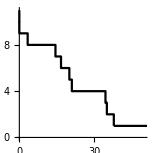

```mathematica
a = dataTAbinding[[All,3]] //Sort[#,Greater]& ; 
dataTAbinding0 = a;
b = Range[1,Length@dataTAbinding] ; 
survivalPlotData = Transpose[{a,b}];
ListStepPlot[survivalPlotData,PlotRange->{{0,50},{All,All}} , survivalPlotOptions[[All]]]
```

```mathematica
(*Range of axis #s... Make more or less to get rid of crowding *){Range[0,50,5],Range[0,10,5] }
```

{{0,5,10,15,20,25,30,35,40,45,50},{0,5,10}}

```mathematica
survivalPlotData = Transpose[{a,b}];
ListStepPlot[survivalPlotData,PlotRange->{{0,50},{All,All}} , survivalPlotOptions[[All]] , Ticks-> {Range[0,50,20],Range[0,10,5] } ]
```

-Graphics-

PERCENTAGE :

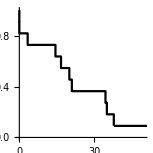

```mathematica
a = dataTAbinding[[All,3]] //Sort[#,Greater]& ; 
b = Range[1,Length@dataTAbinding]  / Length@dataTAbinding; 
survivalPlotData = Transpose[{a,b}];
survivalPlotTA =ListStepPlot[survivalPlotData,PlotRange->{{0,50},{All,All}} , survivalPlotOptions[[All]]]
```

#### TA : Survival plot of all white spots :

```mathematica
(*Use previously determined cutoff to remove any spots that become white too late (after frame 'cutoff' *)
dataTAall = Select [ dataTA,    #[[1]] <cutoff & ] ;
dataTAall//Length
```

20

COUNT :

```mathematica
a = dataTAall[[All,3]] //Sort[#,Greater]& ; 
dataTAall0 = a;
b = Range[1,Length@dataTAall] ; 
survivalPlotData = Transpose[{a,b}]
ListStepPlot[survivalPlotData,PlotRange->{{0,50},{All,All}} , survivalPlotOptions[[All]]]
```

{{999.,1},{980.111,2},{47.7778,3},{40.,4},{37.7778,5},{35.,6},{34.4444,7},{24.4444,8},{22.,9},{22.,10},{21.,11},{20.,12},{16.6667,13},{14.4444,14},{12.2222,15},{7.77778,16},{6.66667,17},{3.33333,18},{0.,19},{0.,20}}

-Graphics-

PERCENTAGE :

```mathematica
a = dataTAall[[All,3]] //Sort[#,Greater]& ; 
b = Range[1,Length@dataTAall]/Length@dataTAall ; 
survivalPlotData = Transpose[{a,b}]//N
survivalPlotTAall = ListStepPlot[survivalPlotData,PlotRange->{{0,50},{All,All}} , survivalPlotOptions[[All]]]
```

{{999.,0.05},{980.111,0.1},{47.7778,0.15},{40.,0.2},{37.7778,0.25},{35.,0.3},{34.4444,0.35},{24.4444,0.4},{22.,0.45},{22.,0.5},{21.,0.55},{20.,0.6},{16.6667,0.65},{14.4444,0.7},{12.2222,0.75},{7.77778,0.8},{6.66667,0.85},{3.33333,0.9},{0.,0.95},{0.,1.}}

-Graphics-

```mathematica
(*USE THIS CODE if I get problems with the graph having a straight line or plateau and messing up  *) 
(*
a = Join[dataTAall[[All,3]] //Sort[#,Greater]&  , {0} ] ;
b = Join[Range[1,Length@dataTAall ]  , {Length@dataTAall }] ;
survivalPlotData = Transpose[{a,b}] ;
ListStepPlot[survivalPlotData,PlotRange->{{0,50},{All,All}} , survivalPlotOptions[[All]]]
*)
```

#### TL : Survival plot of all white spots :

NOTE! I had to add a funky extra # because the plot was a plateau and was messing up ...

```mathematica
(*Not using a 'cutoff' , I know all the spots are OK *)
dataTL0 = dataTL[[All,3]] //Sort[#,Greater]&  (*//#-1108 &  *)
```

{1110.,1110.,1110.,1110.,1110.,1110.}

COUNT :

```mathematica
a = Join[dataTL0, {0} ] ;
b = Join[Range[1,Length@dataTL0 ]  , {Length@dataTL0 }] ;
survivalPlotData = Transpose[{a,b}] ;
ListStepPlot[survivalPlotData,PlotRange->{{0,50},{All,All}} , survivalPlotOptions[[All]]]
```

-Graphics-

PERCENTAGE :

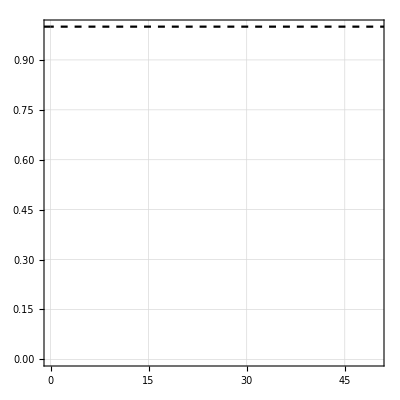

```mathematica
a = Join[dataTL0, {0} ] ;
b = Join[Range[1,Length@dataTL0 ]/ Length@dataTL0  , {1 }] ;
survivalPlotData = Transpose[{a,b}] ;
survivalPlotTL =ListStepPlot[survivalPlotData,PlotRange->{{0,50},{All,All}} , PlotStyle-> {  Black,Dashed},survivalPlotOptions[[All]] ,PlotTheme->"Detailed" ]
```

### Show all plots overlay

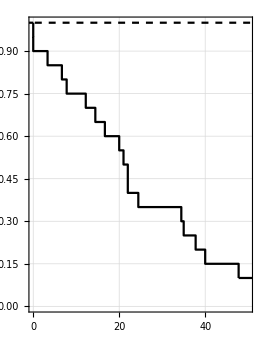

```mathematica
mySurvivalPlot = Show[ survivalPlotTL ,survivalPlotTAall, AspectRatio->1.3,ImageSize->Large]
```

```mathematica
Export["/Volumes/BITTY/_60-90m/mySurvivalPlot.png",mySurvivalPlot]
```

/Volumes/BITTY/_60-90m/mySurvivalPlot.png

# Error Determination: (dev)

### BOOTSTRAPPING for error in Survival Plot :

#### Setting bootstrapping Parameters:

```mathematica
tempdata =  {dataTL0,dataTAall0};
```

```mathematica
sampleSize = Length/@tempdata  
(* sampleSize usually uses the same # as sample size, in my case, number of mRNA*) 
repetitions = 10000;  (* this is repetition of finding the mean of BS data needs to be at least 20 or 30*)
```

{6,20}

#### Setting bootstrapping Parameters:

```mathematica
(* times =  Table[ Range[1,Length@tempdata⟦i⟧] , {i,1,2}] *)
times = Table[Range[1,repetitions],2];
```

```mathematica
tempdata =  {dataTL0,dataTAall0}
```

{{1110.,1110.,1110.,1110.,1110.,1110.},{999.,980.111,47.7778,40.,37.7778,35.,34.4444,24.4444,22.,22.,21.,20.,16.6667,14.4444,12.2222,7.77778,6.66667,3.33333,0.,0.}}

```mathematica
sampleSize = Length/@tempdata  
(* sampleSize usually uses the same # as sample size, in my case, number of mRNA*) 
repetitions = 100;  (* this is repetition of finding the mean of BS data needs to be at least 20 or 30*)
```

{6,20}

```mathematica
a = Table[Table[Table[RandomChoice[tempdata[[i]]],sampleSize⟦i⟧],repetitions ],{i,1,Length@tempdata,1}];
```

```mathematica
Dimensions/@a
```

{{100,6},{100,20}}

```mathematica
Dimensions@a[[2]]
times2 = Table[ Range[1,Length@a[[2,1]]] , Length@a[[2]] ]  / Length@a[[2,1]];
Dimensions@times2
```

{100,20}

{100,20}

```mathematica
sortedAlist = Sort[#,Greater]&/@a[[2]] ;
```

```mathematica
stuff = Table[ Transpose@{sortedAlist ⟦i⟧,  times2⟦i⟧ } , {i,1,Length@a[[2]]}] ;
```

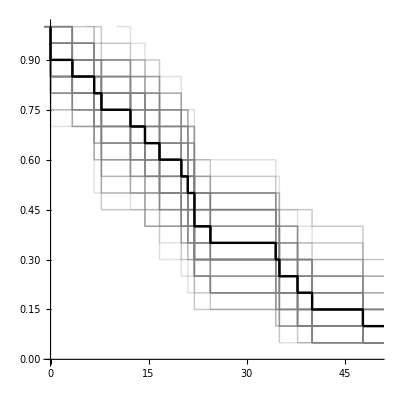

```mathematica
Show[survivalPlotTAall,  ListStepPlot[#,PlotRange->{{0,50},{All,All}}, PlotStyle->{Thin,Opacity[0.25,Gray]}]&/@stuff  ,survivalPlotTAall ]
```